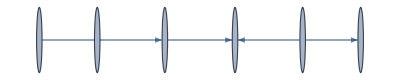

```mathematica
g=Graph[{1<->2,3->4,2->3,5->6,5->4}](*DepthFirstScan[g,{"PrevisitVertex"->(Print["Visiting ",#]&)}]*)
```

```mathematica
FindShortestPath[g,1,4]
```

{1,2,3,4}

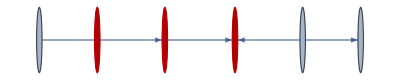

```mathematica
HighlightGraph[Graph[{1,2,3,4,5,6},{{{3,4},{2,3},{5,6},{5,4}},{{1,2}}}],PathGraph[FindShortestPath[g,2,4]]]
```

```mathematica
Import["graph.txt"]
```

Import::nffil: 在 Import 中未找到文件.

$Failed

```mathematica
raw=StringSplit[Import["D:\\wuyudi\\Desktop\\graph.txt"],{" ","\n"}];
row=ToExpression@raw[[1]];
col=ToExpression@raw[[2]];
start=ToExpression@{raw[[3]],raw[[4]]};
end=ToExpression@{raw[[5]],raw[[6]]};
graph=StringSplit[StringJoin@Drop[raw,6],""]~Partition~col
(*graph1=AdjacencyGraph[graph]*)
```

{{1,1,1,1,1},{1,1,2,2,1},{1,2,1,2,1}}

111111122112121

```mathematica
S
```